```mathematica
Solve[(3-x)(-x-4+2k) + 2k==0,x]
```

{{x→1/2 (-1+2 k-√(49-36 k+4 k^2))},{x→1/2 (-1+2 k+√(49-36 k+4 k^2))}}

```mathematica
Solve[49-36 k+4 k ==0,k]
```

{{k→49/32}}

```mathematica
myeq2[k_]:=(1/2 (-1+2 k-√(49-36 k+4 k^2)))(1/2 (-1+2 k+√(49-36 k+4 k^2)))
```

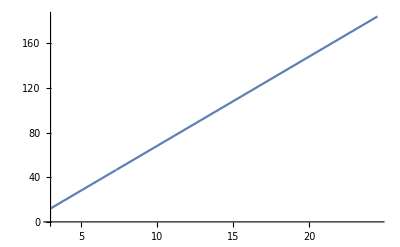

```mathematica
Plot[myeq2[k],{k,49/2,3}]
```

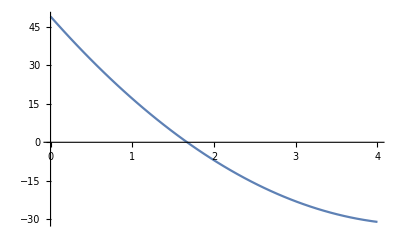

```mathematica
Plot[49-36 k+4 k^2,{k,0,4}]
```

```mathematica
Solve[(-x)(-x-6/k) - (-4)(3-6/k)==0,x]
```

{{x→-3/k-(√3 √(3+8 k-4 k^2))/k},{x→-3/k+(√3 √(3+8 k-4 k^2))/k}}

```mathematica
Solve[3(3+8 k-4 k^2)==0.,k]
```

{{k→-0.322876},{k→2.32288}}

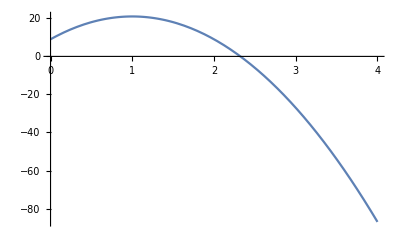

```mathematica
Plot[3(3+8 k-4 k^2), {k,0,4}]
```

```mathematica
myfun[k_]:=(-3/k-(√3 √(3+8 k-4 k^2))/k)
```

```mathematica
myfun2[k_]:=(-3/k+(√3 √(3+8 k-4 k^2))/k)(-3/k-(√3 √(3+8 k-4 k^2))/k)
```

```mathematica
myfun2[2]
```

0

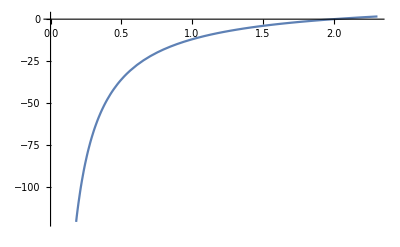

```mathematica
Plot[myfun2[k],{k,0,2.31}]
```

```mathematica
Solve[x^2 + 12 ==0,x]
```

{{x→-2 ⅈ √3},{x→2 ⅈ √3}}

```mathematica
1+Sqrt[7]/2.
```

2.32288